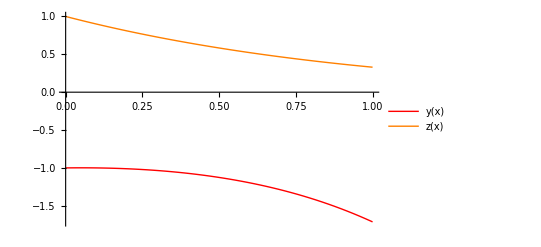

Точное решение системы уравнений имеет вид:

y[x]=-ⅇ^x+x

z[x]=ⅇ^-x

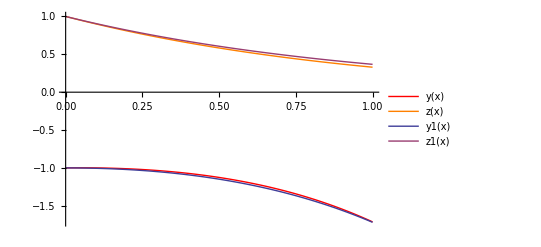

Погрешность приближения для функции y[x] равна: 0.0166244

Погрешность приближения для функции z[x] равна: 0.0215052

```mathematica
(*Зададим правые части системы дифференциальных уравнений*)
f1[x_,y_,z_]=1-1/z;
f2[x_,y_,z_]=1/(y-x);
(*Зададим начальные условия*)
x0=0;
Y={-1};
Z={1};
(*Зададим второй конец отрезка, на котором будем искать решение*)
b=1;
(*Зададим количество частичных отрезков*)
n=50;
(*Найдем шаг разбиения*)
h=(b-x0)/n;
(*Построим разбиение отрезка на частичные*)
X=Table[x0+k*h,{k,0,n}];
(*Реализуем алгоритм метода Эйлера для решения систем дифференциальных уравнений*)
For[k=1,k≤n,k++,
AppendTo[Y,Y[[k]]+h*f1[X[[k]],Y[[k]],Z[[k]]]];
AppendTo[Z,Z[[k]]+h*f2[X[[k]],Y[[k]],Z[[k]]]]
];
(*Выполним интерполяцию найденного решения многочленом Лагранжа*)y[x_]=Sum[Y[[i]]*Product[(x-X[[j]])/(X[[i]]-X[[j]]),{j,1,i-1}]*Product[(x-X[[j]])/(X[[i]]-X[[j]]),{j,i+1,n+1}],{i,1,n+1}];
z[x_]=Sum[ Z[[i]]*Product[(x-X[[j]])/(X[[i]]-X[[j]]),{j,1,i-1}]*Product[(x-X[[j]])/(X[[i]]-X[[j]]),{j,i+1,n+1}],{i,1,n+1}];
(*Построим графики найденного приближенного решения системы*)
GE=Plot[{y[x],z[x]},{x,x0,b},PlotStyle->{Red,Orange},PlotLegends->"Expressions"]
(*Найдем точное решение системы дифференциальных уравнений, используя встроенную функцию*)
Sol=DSolve[{s'[x]==f1[x,s[x],t[x]],t'[x]==f2[x,s[x],t[x]],s[X[[1]]]==Y[[1]],t[X[[1]]]==Z[[1]]},{s[x],t[x]},x];
y1[x_]=s[x]/.Sol[[1,2]];
z1[x_]=t[x]/.Sol[[1,1]];
Print["Точное решение системы уравнений имеет вид:"]
Print["y[x]=",y1[x]]
Print["z[x]=",z1[x]]
(*Построим графики точного и приближенного решения системы в одной системе координат*)
G=Plot[{y1[x],z1[x]},{x,x0,b},PlotLegends->"Expressions"];
Show[GE,G]
(*Найдем погрешность приближения*)
ry=NIntegrate[Abs[y[x]-y1[x]],{x,x0,b}];
rz=NIntegrate[Abs[z[x]-z1[x]],{x,x0,b}];
Print["Погрешность приближения для функции y[x] равна: ",ry]
Print["Погрешность приближения для функции z[x] равна: ",rz]
```